## Capacitance

The capacitance of both trap and feedthough is around 8~16 pF

## Tungsten(kHz,mΩ)

Tungsten is the material we used for 4rod trap, and we test a single tungsten rod at different frequency, due to the skin effect, we can assume the dependence to be R=k √f+b, and then we use the fitting to predict the resistance at 30MHz which is at the same scale we expect to use our helical resonator.

```mathematica
expr=k √f+b0
```

b0+√f k

```mathematica
data={{1,149.2},{5,150.0},{10,150.5},{30,154.3},{50,157.4},{80,163.9},{100,164.4},{150,167.7},{200,170.8},{250,172.7},{300,175.3}}
```

{{1,149.2},{5,150.},{10,150.5},{30,154.3},{50,157.4},{80,163.9},{100,164.4},{150,167.7},{200,170.8},{250,172.7},{300,175.3}}

```mathematica
sol=FindFit[data,expr,{k,b0},f]
```

{k→1.70884,b0→146.34}

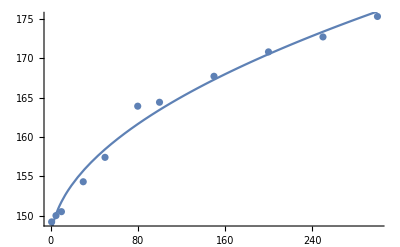

```mathematica
Show[ListPlot@data,Plot[expr/.sol,{f,1,300}]]
```

```mathematica
expr/.sol/.f-> 30000
```

442.32

## feedthrough(Hz,mΩ)

There are multiple types of feedthroughs, including copper, and the one we test is exactly copper feedthrough, according to the corresponding resistance at different frequency, we can fit it into R=k √f+b, so that we can estimate the resistance at the same scale we expect to use, here we predict the resistance 260mΩ at 30MHz.

```mathematica
data2={{100,4.38},{200,4.42},{500,4.50},{1000,4.8},{2000,5.2},{5000,6.0},{10000,7.1},{20000,7.8},{50000,13.3},{80000,18.2},{100000,19.6},{150000,22.2},{200000,23.9},{250000,25.7},{300000,27.2}}
```

{{100,4.38},{200,4.42},{500,4.5},{1000,4.8},{2000,5.2},{5000,6.},{10000,7.1},{20000,7.8},{50000,13.3},{80000,18.2},{100000,19.6},{150000,22.2},{200000,23.9},{250000,25.7},{300000,27.2}}

```mathematica
sol2=FindFit[data2⟦5;;⟧,expr,{k,b0},f]
```

{k→0.046954,b0→2.94889}

```mathematica
Dynamic@Show[ListPlot@data2,Plot[expr/.sol2,{f,1,300*^3}]]
```

```mathematica
expr/.sol2/.f-> 30*^6
```

260.127

## Solder joint(kHz,mΩ)

typical value of the solder joint is R_0=5mΩ at frequency 300kHz, and the final resistance is estimated to be 60mΩ at 30MHz.

```mathematica
data3 = {{1,38 10^-6},{10,30 10^-3},{50,1.45},{100,3.7},{300,5.2}}
```

{{1,19/500000},{10,3/100},{50,1.45},{100,3.7},{300,5.2}}

```mathematica
sol3=FindFit[data3,expr,{k,b0},f]
```

{k→0.350455,b0→-0.62627}

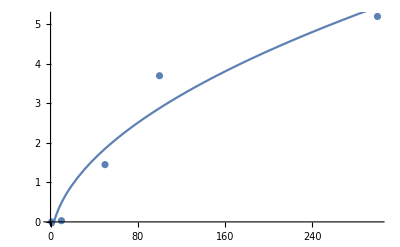

```mathematica
Show[ListPlot@data3,Plot[expr/.sol3,{f,1,300}]]
```

```mathematica
expr/.sol3/.f-> 30000
```

60.0743

## Tips for low contact resistance

### Causes of high contact resistance

1. foreign contamination
2. corrosion of the contact material

High contact resistance leads to overheating, contact welding, high erosion and even no contact

### how to decrease the contact resistance

1. keep the contact surface clean
2. use the correct material, corrosion increases resistance
3. increase the area of contact surface
4. keep the contact cool, any overheating will cause high resistance, prevent welding and excess erosion
5. mechanical wiping action, slight wiping during operation keeps contacts clean